# MSc Data Science - Introduction to Programming (PX 5507) organising data

# Marco Thiel office: Meston Building 332 Email: m.thiel@abdn.ac.uk Tel: 01224 27 3160 Twitter: @DataScienceUoA Office hours: Wednesday 1pm-2:30pm on Zoom Feedback link: https://wolfr.am/11JHosTl0 4 March, 2025

## Overview

This section of the course covers:

Fitting linear models

Fitting nonlinear models

Fitting generalized linear models

Fitting spline curves

## Introduction

#### Terminology

People in many fields use statistics in their work. It is not uncommon for statistical concepts to have different names in different fields. Before proceeding, common terminology is introduced that will be used throughout this course.

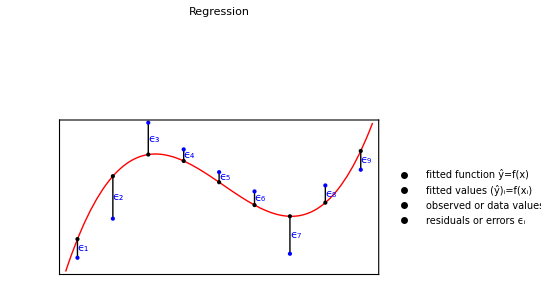

The independent variables: x⃗ = { x_1…, x_n}, the predictor variables

The dependent variable: y, the response variable

In the diagram above, x⃗ is a single variable.

## Introduction: Additional Terminology

Model: the function and optimization criteria (e.g. distributional assumptions) used to approximate the behavior suggested by the data. It will contain one or more parameters to be determined by the fitting process.

Parameters: the values in the model that are not assumed by the predictor or response variables.

## A Useful Tool

You will have occasion to look at long lists of information. So pause briefly to construct a little tool to make the lists more readable.

```mathematica
NiceTable[lis_List,opts:OptionsPattern[Grid]]:= Grid[Partition[lis,4,4,{1,-1},""],{opts,Alignment-> Left}]
```

```mathematica
NiceTable[Range[24]]
```

## Fitting a Linear Model

Your first opportunity to put your function to the test. This is a list of the data files working directory.

```mathematica
NiceTable[FileNames[]]
```

## Import the Data

This brings in the data and arranges it according to species.

```mathematica
fshDat=GatherBy[Import["fishdata.txt","Table"],First];
```

This gives you a count of the various species. The last listed has the largest number of observations, so you can work with that.

```mathematica
Map[{First[#[[1]]],Length[#]}&,fshDat]
```

This gets the data for the last listed species and drops the species index, leaving only the working data.

```mathematica
fshDat[[-1,All,2;;]]//Short
```

## Formatting the Data

This is the same dataset you used in the first notebook of the course. The column headings are species, weight, length 1, length 2, length 3, height, thickness. You have already eliminated the species index. You will estimate the weight of a fish from its physical dimensions. Therefore, the other issues you need to adjust are moving the weight to the end of the list and dealing with the height and weight. Height and weight are given as a percent of the third length, L3. You do this using ReplaceAll.

```mathematica
wrkDat=(fshDat[[-1,All,2;;]]/.{{wt_,L1_,L2_,L3_,ht_,thk_}:> {L1,L2,L3,ht L3/100,thk L3/100,wt}});
```

Begin by looking at the weight as a function of the L3 value.

```mathematica
ListPlot[wrkDat[[All,{3,-1}]]]
```

## Fitting the Data

```mathematica
?LinearModelFit
```

This fits the data to a cubic polynomial. Give the fitted model a name for use in subsequent investigations.

```mathematica
wtEst1=LinearModelFit[wrkDat[[All,{3,-1}]],x^Range[0,3],x]
```

Visualize the fit.

```mathematica
Plot[wtEst1[x],{x,8,48},Epilog-> {Point[wrkDat[[All,{3,-1}]]]}]
```

## Getting Information about the Fit

The FittedModel contains a great deal of information. You can get a list of what is available using “Properties” as an argument to the model.

```mathematica
Framed[NiceTable[Style[#,14,"Text"]&/@wtEst1["Properties"]],RoundingRadius-> 12,FrameMargins-> 15]
```

Look at the ANOVA table and adjusted R-squared values for your fit.

```mathematica
wtEst1[{"ANOVATable","AdjustedRSquared"}]
```

Visualize the fit with mean prediction bands. If the join of the function with the prediction bands is used directly in the Plot function, it will have to be wrapped in Evaluate.

```mathematica
With[{expr= Join[{wtEst1[x]},wtEst1["MeanPredictionBands"]]},Plot[expr,{x,8,48},Epilog-> {Point[wrkDat[[All,{3,-1}]]]},Filling-> {2-> {3}}]]
```

## Alternate Models

In the previous example, you selected two columns from the data and a single predictor variable for the model. You can use the full dataset and give a select set of basis vectors for your model.

Fit the same model as before, using the full dataset.

```mathematica
wtEst2=LinearModelFit[wrkDat,L3^Range[0,3],{L1,L2,L3,Ht,Thck}]
```

Note the only difference is the way in which you ask for the result.

```mathematica
Column[{wtEst1[L3],wtEst2[L1,L2,L3,Ht,Thck]}]
```

## Alternate Models

Using the information from the previous slide, you can fit several models at the same time using the Table function. Assigning a name to the list will allow you to get diagnostics for the various fits.

```mathematica
multiFit= Table[LinearModelFit[wrkDat,basis,{L1,L2,L3,Ht,Thck}],{basis,{L3^Range[0,3],{L3,Ht},{L3,Thck},Flatten[{L3^Range[0,2],Ht}]}}]
```

The last model in the list accounts for up to 98% of the variation in the weights of the fish.

```mathematica
Through[multiFit["AdjustedRSquared"]]
```

```mathematica
Through[multiFit["AIC"]]
```

## Alternate Models

Here are ANOVA tables for the first and last models in your set.

```mathematica
Through[multiFit[[{1,-1}]]["ANOVATable"]]
```

Here is a visualization of the last model in the list.

```mathematica
Show[{Plot3D[Through[multiFit[[{-1}]][0,0,L3,Ht,0]],{L3,8,48},{Ht,2,13}],Graphics3D[ {Red,PointSize[Medium],Point[wrkDat[[All,{3,4,6}]]]}]}]
```

## Alternate Models

Having decided on a model, simplify things by constructing a model using only the necessary variables.

```mathematica
wtEst3= LinearModelFit[wrkDat[[All,{3,4,6}]],Flatten[{L3^Range[0,2],Ht}],{L3,Ht}]
```

```mathematica
ListPlot[wtEst3["FitResiduals"]]
```

A large adjusted R^2 does not necessarily indicate the Gauss–Markov conditions are satisfied.

```mathematica
Style[Column[DistributionFitTest[wtEst3["StudentizedResiduals"],NormalDistribution[μ,σ],{"TestDataTable","FittedDistribution","TestConclusion"}]],"Text"]
```

```mathematica
Clear[wtEst1,wtEst2,wtEst3,multifit,wrkDat,fshDat]
```

## Nonlinear Model Fitting

Linear models are fitted using linear algebra, a process that is, in most cases, robust and fast. Nonlinear models, on the other hand, require the construction of a merit function and then minimizing the merit function based on varying a set of parameters present in the model. This process can be slow and often requires more attention on the part of the statistician.

The Excel file you will use for your first example was obtained from the US Department of Energy’s website: www.eia.doe.gov/cneaf/electricity/epm/table1_1.html. It contains data on net power generation by energy source for the years 1994 through 2008. This dataset has been replaced by a more detailed set of files on the current website, but is included in the datasets for the course.

```mathematica
FileNames["*.xls"]
```

```mathematica
electricData= Import["epmxlfile1_1.xls",{"Data",1}];
```

```mathematica
Dimensions[electricData]
```

You might want to look at the first few rows to get a sense of how it looks in the Wolfram Language.

```mathematica
Take[electricData,5]
```

```mathematica
TableView[electricData,ImageSize-> 14 72]
```

## Excel Spreadsheets: Filtering the Data

You will look at renewables up through the year 2010. First, determine the number of the column containing the data you want to use.

The information you want is in the ninth column.

```mathematica
Position[electricData,"Other Renewables[4]"]
```

Referring to your table above, you see you want rows 4 through 57 and columns 1 and 9.

```mathematica
renewables=electricData[[4;;57,{1,9}]];
TableView[renewables]
```

Using pattern matching, convert the strings to numbers and extract only the yearly totals.

```mathematica
yearTots=Cases[renewables,{_?NumericQ|"Total",_?NumericQ}]
```

Using replacement rules, “clean up” the rows corresponding to the years 2006, 2007, and 2008.

```mathematica
results=ReplacePart[yearTots,{{-3,1}-> 2006.,{-2,1}->2007.,{-1,1}->2008.}]
```

## Looking at the Data

Now that you have cleaned up the data, you can look at the form of the data and determine a model. Apart from the year 2001, this looks a lot like exponential growth.

```mathematica
dataplot=ListLinePlot[results,Mesh-> All,PlotMarkers-> Automatic]
```

## NonlinearModelFit

Use NonlinearModelFit to see if this gives a reasonable fit to the data. Note the translation of the variable by c, to get the curve to fit. Raising ⅇ to a large power is going to give misleading information.

```mathematica
?NonlinearModelFit
```

Note the use of start values for the translation value c.

```mathematica
model=NonlinearModelFit[results,a+ⅇ^(b (t-c)),{a,b,{c,1990}},t]
```

```mathematica
model["BestFit"]
```

The fit appears to be a good one.

```mathematica
Show[
Plot[model[t],{t,1993.5,2008.5},PlotStyle->{Pink,Thick},PlotRange->All],
dataplot
]
```

## Robust Regression

The 2001 value in the data seems inconsistent with the rest of the values; it could have been recorded incorrectly, or it could be an outlier. In either case, you might want to use robust regression to reduce the influence of that observation on the fit. That is done in NonlinearModelFit using the option Weights.

```mathematica
Framed[NiceTable[Style[#,14,"Text"]&/@Options[NonlinearModelFit]],RoundingRadius-> 8]
```

Fit using the absolute value norm.

```mathematica
model2=NonlinearModelFit[results,a+ⅇ^(b (t-c)),{a,b,{c,1990}},t,Weights-> (Norm[#,1]&)];
```

```mathematica
{model["BestFit"],model2["BestFit"]}
```

The results seem very similar, but they are different.

```mathematica
GraphicsRow[{Show[
{Plot[model[t],{t,1993.5,2008.5},PlotStyle->{Pink,Thick},PlotRange->All],
dataplot},PlotLabel-> Style["model",14,Bold]
],Show[{
Plot[model2[t],{t,1993.5,2008.5},PlotStyle->{Pink,Thick},PlotRange->All],
dataplot},PlotLabel-> Style["model2",14,Bold]
],Plot[{model2[t]-model[t]},{t,1993.5,2008.5},PlotStyle->{Pink,Thick},PlotRange->All,PlotLabel-> Style["model2-model",14,Bold]]},ImageSize-> 12 72]
```

## Some Diagnostics

Because you are using a nonlinear model here, the property list is shorter than with LinearModelFit.

```mathematica
NiceTable[Style[#,12,"Text"]&/@model["Properties"]]
```

When you look at the diagnostics, you see the real differences.

```mathematica
model[{"ANOVATable","FitCurvatureTable","ParameterBias","AICc"}]
```

```mathematica
model2[{"ANOVATable","FitCurvatureTable","ParameterBias","AICc"}]
```

```mathematica
Clear[model,model2]
```

## Fitting Theoretical Models

In many disciplines–physics, chemistry, and engineering, for example–one needs to test theoretical models. The Wolfram Language provides a very nice framework for doing that sort of thing. For example, a first-order approximation to the velocity of a rocket at time t should satisfy the solution to the differential equation:

dv/dt=(β s)/(m_0−β t)−g,
v_0=0

where g is acceleration due to gravity, m_0 is initial mass, s is exhaust velocity, and β is fuel consumption.

This model has a symbolic solution, so you could take that approach, but more sophisticated models may not have a symbolic solution. You can illustrate that situation and assume there is no symbolic solution available. Confidence is assumed for estimates of all the parameters except for β. You can attempt to estimate β from observed (in this case simulated) data.

Bring in your data.

```mathematica
FileNames["*.dat"]
```

```mathematica
rcktDat= Import["rcktDat.dat"];
```

```mathematica
Dimensions[rcktDat]
```

```mathematica
InputForm/@rcktDat[[;;3]]
```

```mathematica
rcktDat=Flatten[rcktDat/.{str_String:> ToExpression@StringSplit[str,","]},1]
```

## Fitting Theoretical Models

Begin by creating a ParametricFunction.

```mathematica
sol=ParametricNDSolve[{v'[t]==-9.8+(700 β)/(10000-t β),v[0]==0},v,{t,0,60},{β}]
```

Use the parametric function in NonlinearModelFit. Note the positions of the parameter β and the variable t.

```mathematica
rcktModl=Quiet[NonlinearModelFit[Most[rcktDat],v[β][t]/.sol,{β},t]]
```

Visualize the results.

```mathematica
Plot[rcktModl[t],{t,0,60},Epilog-> Point[rcktDat]]
```

## Diagnostics from the Fit

As with any fit, you should look at the diagnostics. Even though you have obtained your solution using interpolating functions, you still have diagnostics available from the fit.

```mathematica
rcktModl["ANOVATable"]
```

```mathematica
rcktModl[{"ParameterTable","ParameterBias"}]
```

```mathematica
ListPlot[rcktModl["FitResiduals"],Filling-> Axis]
```

```mathematica
Clear[rcktModl,rcktDat]
```

## Piecewise Models

Many of the datasets included with the course come from the government agency NIST.

www.itl.nist.gov/div898/strd/general/dataarchive.html

The data in the set used here was collected by A. Filippelli at NIST, but no information is provided as to what was measured. The NIST site does indicate the set was obtained from observation, and is not a generated set.

Bring in the data.

```mathematica
filipDat= Sort[Import["filipdata.txt","Table"]];
```

Check the dimensions.

```mathematica
Dimensions[filipDat]
```

Visualize the data.

```mathematica
ListPlot[filipDat,GridLines-> Automatic]
```

## Constructing a Piecewise Continuous Model

Fit three straight lines to the data. Straight lines can be expressed in the form mx+b, and the intersection of two such lines can be given as a function of the two slopes and intercepts.

```mathematica
Clear[x,m1,m2,m3,b1,b2,b3]
```

Use Set and not SetDelayed here because you do not want to reconstruct the model every time it is used.

```mathematica
mdl[x,{m1,m2,m3,b1,b2,b3}]=With[{sol1= Solve[m1 x +b1==m2 x + b2,x],sol2= Solve[m2 x + b2==m3 x + b3,x]},
sols= Join[sol1,sol2];
{int1,int2}=x/.sols;
Piecewise[{{m1 x + b1, x<int1}, {m2 x + b2, int1≤ x<int2}, {m3 x + b3, int2≤ x}}]];
```

Use the model in NonlinearModelFit. Use constraints with the model, and specify start values for the parameters estimated from the plot above.

```mathematica
pcwsMdl=NonlinearModelFit[filipDat,{mdl[x,{m1,m2,m3,b1,b2,b3}],-8.25<(-b1+b2)/(m1-m2)<-6.4,-6.4<(-b2+b3)/(m2-m3)<-5.9},{{m1,.1},{m2,1.0},{m3,.1},{b1,.75},b2,{b3,.87}},x]
```

## Visualizing the Results

The fit looks good, and you can get diagnostics from the fit.

The solution curve with the data points.

```mathematica
pcwsPlt=Plot[pcwsMdl[t],{t,-9,-3},Epilog-> {Red,Point[filipDat]},PlotLabel-> Style["Piecewise Model",18,Bold]]
```

A look at the residuals.

```mathematica
ListPlot[pcwsMdl["FitResiduals"]]
```

## A Linear Approach

The piecewise model used previously is not a linear model, as it is not expressed as a linear combination of basis vectors. If you knew precisely the locations of the intersections of the lines, you could write a set of basis vectors that would work, but you do not. Take advantage of smoothing splines. By using nonuniform knot spacings, you can generate linear b-splines (NURBS) that will do what you want, using the Wolfram Language’s BSplineBasis function.

Visualize the data again, and pay particular attention to the positions of the abrupt changes of direction in the data.

```mathematica
ListPlot[filipDat,GridLines-> Automatic]
```

The data goes approximately from -9 to -3 with sharp changes in direction around -7.2 and -6.1.

Generate the spline basis functions.

```mathematica
knts={-9,-7.2,-6.1,-3};
splns=Table[BSplineBasis[{1,knts},i,x],{i,0,1}]
```

Visualize the result.

```mathematica
Plot[splns,{x,-9,-3},GridLines-> Automatic]
```

## A Utility Function and a Fit

Here is a function that will make things easier. It creates the basis for the fit and then applies LinearModelFit to the data and the basis set. You can use this as a model to create a function of your own to handle the sorts of cases you work with most often.

```mathematica
SplineModel[data_,knots_,dom:{x_,xmin_,xmax_},bs_List,deg_Integer]:=
Block[{basis,allKnots,n},
n=Length[knots]+2;
basis=bs~Join~Table[BSplineBasis[{deg,Join[{xmin},knots,{xmax}]},i,x],{i,0,n-3}];
LinearModelFit[data,basis,x]
]
```

Fit the data.

```mathematica
smoothFit=SplineModel[filipDat,{-7.2,-6.1},{x,-9,-3},x^Range[0,1],1]
```

## Visualizing the Two Approaches

This shows plots of the two different fits.

```mathematica
GraphicsRow[{pcwsPlt,Plot[smoothFit[t],{t,-9,-3},Epilog-> {Red,Point[filipDat]},PlotLabel-> Style["Spline Smoothing Model",18,Bold]]},ImageSize-> 10 72]
```

A table of results.

```mathematica
Grid[{{Style["piecewise model","Subsection"],Style["spline smoothing model","Subsection"]},{Style[StringForm["Adjusted R squared `1`",NumberForm[pcwsMdl["AdjustedRSquared"],{5,6}]],"Text"],Style[StringForm["Adjusted R squared `1`",NumberForm[smoothFit["AdjustedRSquared"],{5,6}]],"Text"]},{ListPlot[pcwsMdl["FitResiduals"],PlotLabel-> Style["fit residuals","Text"],ImageSize-> Medium],ListPlot[smoothFit["FitResiduals"],PlotLabel-> Style["fit residuals","Text"],ImageSize-> Medium]}},Frame-> All]
```

```mathematica
Clear[smoothFit,pcwsMdl,filipDat]
```

## Initialization

This is a text cell.

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"DataDir"}]]
```